```mathematica
data=Import["C:/Users/Ian/Desktop/gravlensingproject/data.csv"];
theta=data⟦;;,1⟧;
ellipticity=data⟦;;,2⟧;
σellipticity=data⟦;;,3⟧;
```

```mathematica
H0=69.32 Quantity[, ("Kilometers")/("Megaparsecs" "Seconds")];
ρcrit=UnitConvert[(3 H0^2)/(8π Quantity[, "GravitationalConstant"]),"SI"];
DL=1 Quantity[, "Gigaparsecs"];
DS=3 Quantity[, "Gigaparsecs"];
criticalSurfaceDensity=UnitConvert[Quantity[, "SpeedOfLight"]^2/(4π Quantity[, "GravitationalConstant"])*DS/((DS-DL)*DL),"SI"];
```

## NFW Fit

```mathematica
rs=UnitConvert[M200^(1/3)/c((3(Quantity[, "SolarMass"]))/(800π ρcrit))^(1/3),"SI"];
θs=rs/DL*QuantityMagnitude[Quantity[, "Radians"],Quantity[, "ArcSeconds"]];
δc=200/3*c^3/(Log[1+c]-c/(1+c));
```

```mathematica
NFWsurfaceDensity=(2δc*ρcrit*rs)/((θ/θs)^2-1)(1-2/(√((θ/θs)^2-1))ArcTan[√((θ/θs-1)/(θ/θs+1))]) ;
NFWaverageSurfaceDensity=(4δc*ρcrit*rs)/(θ/θs)^2(2/(√((θ/θs)^2-1))ArcTan[√((θ/θs-1)/(θ/θs+1))]+Log[(θ/θs)/2]) ;
NFWconvergence=NFWsurfaceDensity/criticalSurfaceDensity;
NFWshear=Simplify[Expand[(NFWaverageSurfaceDensity-NFWsurfaceDensity)/criticalSurfaceDensity]];
NFWreducedShear=NFWshear/(1-NFWconvergence);
NFWellipticity=(2*NFWreducedShear)/(1+NFWreducedShear^2);
```

```mathematica
NFWchiSquared=Total[((ellipticity-Re[(NFWellipticity/.θ->theta)])/σellipticity)^2];
```

```mathematica
NFWchiSquared/.{M200->10^15,c->10}
```

39.1914

```mathematica
NFWfit=NMinimize[{NFWchiSquared/.M200->10^logM200,10<logM200<20,0<c<50},{logM200,c},PrecisionGoal->10,WorkingPrecision->10]
```

{38.0611762,{logM200→14.98657103,c→10.16501617}}

```mathematica
NFWlogchiSquared2D=Flatten[Table[{logM200,c,Log[10,NFWchiSquared/.{M200->10^logM200}]},{logM200,14.7,15.3,.01},{c,.1,20,.5}],1];
```

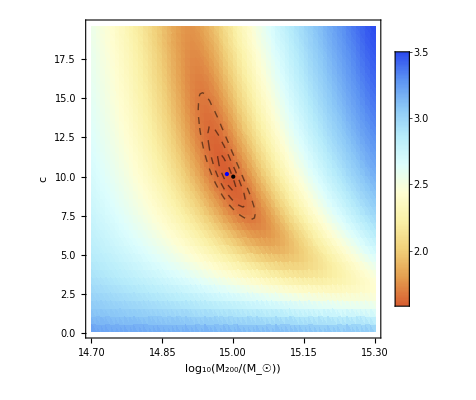

```mathematica
Show[
ListDensityPlot[NFWlogchiSquared2D,PlotRange->All,ColorFunction->ColorData[{"LightTemperatureMap","Reverse"}],PlotLegends->Automatic],
ListContourPlot[NFWlogchiSquared2D,PlotRange->All,Contours->Log[10,NFWfit⟦1⟧+{1,4,9}],ContourShading->None,ContourStyle->Dashed],
Graphics[{Blue,Point[{logM200,c}/.NFWfit⟦2⟧],Black,Point[{15,10}]}],
FrameLabel->{"log_10(M_200/(M_☉))","c"}]
```

## Isothermal Fit

```mathematica
r200=UnitConvert[M200^(1/3)((3 Quantity[, "SolarMass"])/(800π ρcrit))^(1/3),"SI"];
σ2=(M200 Quantity[, "SolarMass"]Quantity[, "GravitationalConstant"] /Quantity[, "Meters"])/Expand[2(r200-DL θc ArcTan[r200/(DL θc)])*1/Quantity[, "Meters"]];
```

```mathematica
ISOsurfaceDensity=σ2/(2 Quantity[, "GravitationalConstant"]DL √(θ^2+θc^2)) ;
ISOaverageSurfaceDensity=(σ2(√(θ^2+θc^2)-θc))/(2 Quantity[, "GravitationalConstant"]DL θ^2) ;
ISOconvergence=ISOsurfaceDensity/criticalSurfaceDensity;
ISOshear=Simplify[Expand[(ISOaverageSurfaceDensity-ISOsurfaceDensity)/criticalSurfaceDensity]];
ISOreducedShear=ISOshear/(1-ISOconvergence);
ISOellipticity=(2*ISOreducedShear)/(1+ISOreducedShear^2)/.{θ->t*QuantityMagnitude[Quantity[, "ArcSeconds"],Quantity[, "Radians"]],θc->tc*QuantityMagnitude[Quantity[, "ArcSeconds"],Quantity[, "Radians"]]};
```

```mathematica
ISOchiSquared=Total[((ellipticity+(ISOellipticity/.t->theta))/σellipticity)^2];
```

```mathematica
ISOfit=NMinimize[{ISOchiSquared/.M200->10^logM200,10<logM200<20,0<tc<1000},{logM200,tc},PrecisionGoal->10,WorkingPrecision->10]
```

{42.65769787,{logM200→15.74465864,tc→140.4312288}}

```mathematica
ISOlogchiSquared2D=Flatten[Table[{logM200,tc,Log[10,ISOchiSquared/.M200->10^logM200]},{logM200,15.4,16,.01},{tc,100,200,5}],1];
```

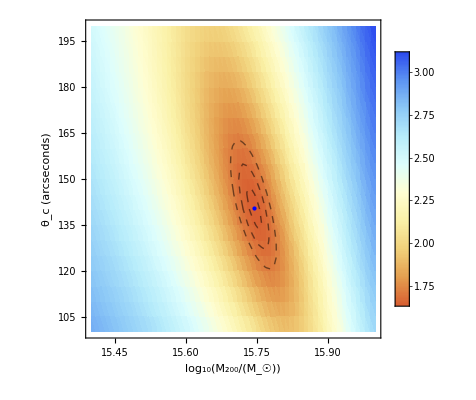

```mathematica
Show[
ListDensityPlot[ISOlogchiSquared2D,PlotRange->All,ColorFunction->ColorData[{"LightTemperatureMap","Reverse"}],PlotLegends->Automatic],
ListContourPlot[ISOlogchiSquared2D,PlotRange->All,Contours->Log[10,ISOfit⟦1⟧+{1,4,9}],ContourShading->None,ContourStyle->Dashed],
Graphics[{Blue,Point[{logM200,tc}/.ISOfit⟦2⟧]}],
FrameLabel->{"log_10(M_200/(M_☉))","θ_c (arcseconds)"}
]
```

## Comparison

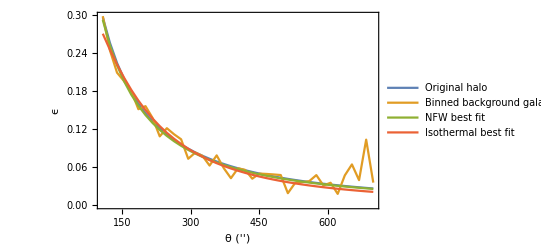

```mathematica
ListLinePlot[{
Transpose[{theta,ellipticityNFW/.{θ->theta,M200->10^15,c->10}}],
Transpose[{theta,ellipticity}],
Transpose[{theta,((ellipticityNFW/.M200->10^logM200)/.NFWfit⟦2⟧)/.θ->theta}],
Transpose[{theta,((-ISOellipticity/.M200->10^logM200)/.ISOfit⟦2⟧)/.t->theta}]},
PlotRange->All,PlotLegends->{"Original halo","Binned background galaxies","NFW best fit","Isothermal best fit"},Frame->True,FrameLabel->{"θ ('')","ϵ"}]
```